```mathematica
<<sneg`;
```

sneg 1.252 Copyright (C) 2002-2019 Rok Zitko

a::shdw: Symbol a appears in multiple contexts {Sneg`,Global`}; definitions in context Sneg` may shadow or be shadowed by other definitions.

```mathematica
snegfermionoperators[c,d];
```

```mathematica
n=2;
ddd=2/n;
bz=qsbasisvc[{c[1],c[2],d[]}];
bz=Map[{#[[1]]+{n+1,0},#[[2]]}&,bz];
```

```mathematica
-1.+ddd/2
```

-0.5

```mathematica
ClearAll[ϵ];U=.;ϵd=.;t=.;V=.;
H=U hubbard[d[]]+ϵd number[d]+U/2+Sum[ϵ[i] number[c[i]],{i,n}]+V Sum[nc[c[CR,i,UP],c[CR,i,DO],c[AN,j,DO],c[AN,j,UP]],{i,n},{j,n}]+t Sum[hop[c[i],d[]],{i,n}]//Expand
ϵ[1]=-1/2;
ϵ[2]=1/2;
U=10;
ϵd=-U/2;
gamma=1;
V=Sqrt[2. gamma/Pi]
t=V/Sqrt[n]
α=1;
V=-α ddd
H
mats=makematricesbzvc[H,bz]
```

U/2+t c_(1↓)^†·d_↓^+t c_(1⇑)^†·d_⇑^+t c_(2↓)^†·d_↓^+t c_(2⇑)^†·d_⇑^+t d_↓^†·c_(1↓)^+t d_↓^†·c_(2↓)^+ϵd d_↓^†·d_↓^+t d_⇑^†·c_(1⇑)^+t d_⇑^†·c_(2⇑)^+ϵd d_⇑^†·d_⇑^-V c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-U d_↓^†·d_⇑^†·d_↓^·d_⇑^+c_(1↓)^†·c_(1↓)^ ϵ[1]+c_(1⇑)^†·c_(1⇑)^ ϵ[1]+c_(2↓)^†·c_(2↓)^ ϵ[2]+c_(2⇑)^†·c_(2⇑)^ ϵ[2]

0.797885

0.56419

-1

5-1/2 c_(1↓)^†·c_(1↓)^+0.56419 c_(1↓)^†·d_↓^-1/2 c_(1⇑)^†·c_(1⇑)^+0.56419 c_(1⇑)^†·d_⇑^+1/2 c_(2↓)^†·c_(2↓)^+0.56419 c_(2↓)^†·d_↓^+1/2 c_(2⇑)^†·c_(2⇑)^+0.56419 c_(2⇑)^†·d_⇑^+0.56419 d_↓^†·c_(1↓)^+0.56419 d_↓^†·c_(2↓)^-5 d_↓^†·d_↓^+0.56419 d_⇑^†·c_(1⇑)^+0.56419 d_⇑^†·c_(2⇑)^-5 d_⇑^†·d_⇑^+c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-10 d_↓^†·d_⇑^†·d_↓^·d_⇑^

{{{0,0},{{5}}},{{1,1/2},{{0.,0.56419,0.56419},{0.56419,5.5,0.},{0.56419,0.,4.5}}},{{2,0},{{5.,0.797885,0.797885,0.,0.,0.},{0.797885,0.5,0.,0.797885,0.56419,0.},{0.797885,0.,-0.5,0.,0.56419,0.797885},{0.,0.797885,0.,5.,0.,-1.},{0.,0.56419,0.56419,0.,5.,0.},{0.,0.,0.797885,-1.,0.,3.}}},{{2,1},{{0.5,0.,-0.56419},{0.,-0.5,0.56419},{-0.56419,0.56419,5.}}},{{3,1/2},{{5.5,0.,-0.56419,-0.398942,0.,-0.690988,0.,0.},{0.,4.5,0.,-0.398942,-0.56419,0.690988,0.,0.},{-0.56419,0.,0.,0.,-1.,0.,0.56419,0.},{-0.398942,-0.398942,0.,0.,0.,0.,-0.398942,-0.398942},{0.,-0.56419,-1.,0.,-2.,0.,0.,0.56419},{-0.690988,0.690988,0.,0.,0.,0.,0.690988,-0.690988},{0.,0.,0.56419,-0.398942,0.,0.690988,4.5,0.},{0.,0.,0.,-0.398942,0.56419,-0.690988,0.,3.5}}},{{3,3/2},{{0}}},{{4,0},{{5.,0.,-1.,0.797885,0.,0.},{0.,5.,0.,-0.56419,-0.56419,0.},{-1.,0.,3.,0.,0.797885,0.},{0.797885,-0.56419,0.,-0.5,0.,0.797885},{0.,-0.56419,0.797885,0.,-1.5,0.797885},{0.,0.,0.,0.797885,0.797885,3.}}},{{4,1},{{5.,-0.56419,0.56419},{-0.56419,-0.5,0.},{0.56419,0.,-1.5}}},{{5,1/2},{{4.5,0.,-0.56419},{0.,3.5,-0.56419},{-0.56419,-0.56419,-2.}}},{{6,0},{{3}}}}

```mathematica
{qn,hh}=mats[[5]];
qn
e3=Sort@Eigenvalues[hh]
FullForm[e3]
{val,vec}=Transpose@Sort@Transpose@Eigensystem[hh];
```

{3,1/2}

{-2.51293,-0.443828,-0.140417,0.341,3.69239,4.54993,4.8179,5.69595}

List[-2.51293,-0.443828,-0.140417,0.341,3.69239,4.54993,4.8179,5.69595]

```mathematica
ψ=vec[[1]].bz[[5,2]];
expvvc[number[d],ψ]
nc[conj[ψ],ap[number[d],ψ]]
expvvc[number[c[1]],ψ]
expvvc[number[c[2]],ψ]
expvvc[nc[d[CR,UP],d[CR,DO]],ψ]
```

0.997624

0.997624

1.70761

0.294764

0.

```mathematica
(* site pairing *)
V Sqrt[expvvc[hubbard[c[1]],ψ]-expvvc[number[c[1],UP],ψ]expvvc[number[c[1],DO],ψ]]
V Sqrt[expvvc[hubbard[c[2]],ψ]-expvvc[number[c[2],UP],ψ]expvvc[number[c[2],DO],ψ]]
(* amplitudes *)
Sqrt[expvvc[nc[d[CR,UP],d[CR,DO],d[AN,DO],d[AN,UP]],ψ]]
Sqrt[expvvc[nc[d[AN,DO],d[AN,UP],d[CR,UP],d[CR,DO]],ψ]]
% %%
Sqrt[expvvc[nc[c[CR,1,UP],c[CR,1,DO],c[AN,1,DO],c[AN,1,UP]],ψ]]
Sqrt[expvvc[nc[c[AN,1,DO],c[AN,1,UP],c[CR,1,UP],c[CR,1,DO]],ψ]]
% %%
```

-0.347853

-0.347634

0.0803563

0.0939835

0.00755216

0.92194

0.377308

0.347856

```mathematica
val
```

{-2.51293,-0.443828,-0.140417,0.341,3.69239,4.54993,4.8179,5.69595}

```mathematica
g[i_,j_]:=nc[conj[vec[[i]].bz[[5,2]]],ap[number[d[]],vec[[j]].bz[[5,2]]]];
```

```mathematica
g[1,1]
```

0.997624

```mathematica
gij=Table[g[i,j],{i,8},{j,8}]
```

{{0.997624,0.00381294,0.0200803,0.000204141,-0.0958772,0.0307707,0.0659822,-0.0193301},{0.00381294,0.981939,-0.00688488,0.004075,0.180706,-0.201704,0.0535184,-0.108091},{0.0200803,-0.00688488,0.993664,-0.0093159,0.101549,0.124322,0.0214891,-0.062364},{0.000204141,0.004075,-0.0093159,0.998374,-0.00667669,0.0536524,-0.0569611,0.0484652},{-0.0958772,0.180706,0.101549,-0.00667669,0.0776811,-0.163098,-0.113157,-0.1389},{0.0307707,-0.201704,0.124322,0.0536524,-0.163098,1.00314,0.936587,0.167788},{0.0659822,0.0535184,0.0214891,-0.0569611,-0.113157,0.936587,1.02324,-0.202474},{-0.0193301,-0.108091,-0.062364,0.0484652,-0.1389,0.167788,-0.202474,1.92434}}

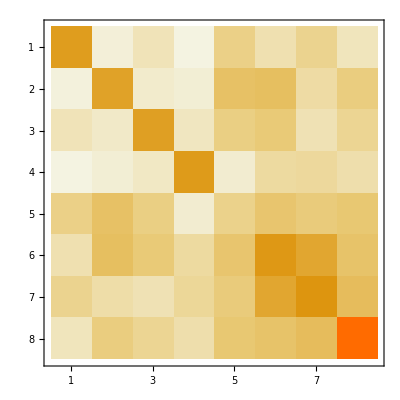

```mathematica
MatrixPlot[gij^2]
```

```mathematica
(* Diagonal: impurity occupancies *)
Table[g[i,i],{i,8}]
```

{0.997624,0.981939,0.993664,0.998374,0.0776811,1.00314,1.02324,1.92434}

```mathematica
(* static charge susceptibility *)
```

```mathematica
Table[2g[1,i]^2/(val[[i]]-val[[1]]),{i,2,8}]
Total[%]
```

{0.000014053,0.000339908,2.92044×10^-8,0.00296276,0.000268117,0.00118777,0.0000910365}

0.00486367